-b z^8+z^17+λ/9

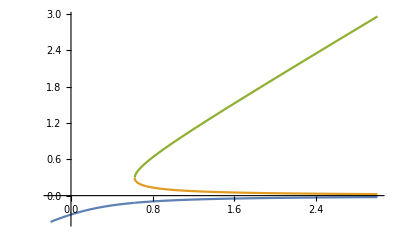

```mathematica
Clear["Global`*"]

n=1;
m=9;
eqn=z^(2 m-n)+λ n/m - b z^(m-n);
eqn
sol=Solve[eqn==0,z];
solK[β_,Λ_,k_]:=(z/.sol)[[k]]/.{b->β,λ->Λ}

l=1;
Plot[{solK[b,l,1]^m,solK[b,l,2]^m,solK[b,l,3]^m},{b,-0.2,3}]
```

```mathematica
Reduce[solK[b,l,2]]
```

Reduce::naqs: Root[1-9 b #1^8+9 #1^17&,2] is not a quantified system of equations and inequalities.

Reduce[Root[1-9 b #1^8+9 #1^17&,2]]

Root[l^3-27 b^3 #1^2+81 b^2 #1^3-81 b #1^4+27 #1^5&,2]

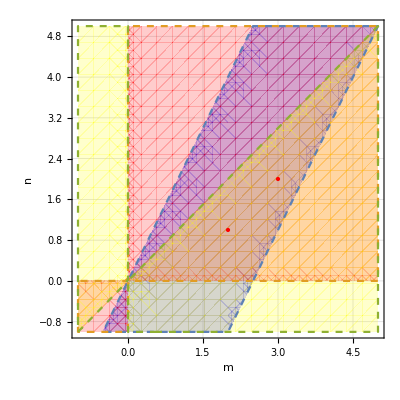

```mathematica
Clear["Global`*"]
pts={m,n}/.List@ToRules@Reduce[0<2m-n<5&&n/m>0&&n/m<1&&n>0,{n,m},Integers];
RegionPlot[{0<2m-n<5,n/m>0,n/m<1},{m,-1,5},{n,-1,5},
Epilog->{Red,Point@pts},
FrameLabel->Automatic,
GridLines->Automatic,
BoundaryStyle->Dashed,
PlotStyle->{Directive[Opacity[0.2,Blue]], Directive[Opacity[0.2,Red]], Directive[Opacity[0.2,Yellow]]}]
```

{{1,2},{2,3}}

{{1,2},{2,3}}

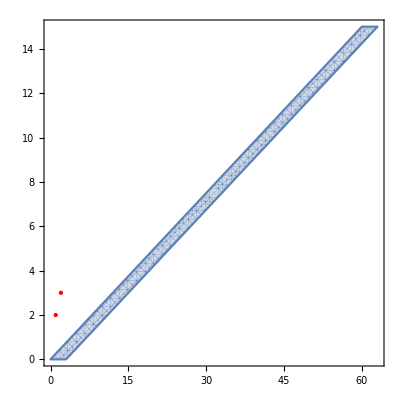

```mathematica
Clear["Global`*"]
pts=DeleteCases[Flatten[Outer[Boole[4 #2≤#1≤4 #2+3] {#1,#2}&,Range[0,63],Range[0,15]],1],{0,0}];

DeleteCases[Flatten[Outer[Boole[2 #2 - #1<5&& #1/#2>0 && #1/#2<1] {#1, #2} &, Range[1,10],Range[1,10]],1],{0,0}]


RegionPlot[x≥4 y&&x≤4 y+3,{x,0,63},{y,0,15},Epilog->{Red,Point@pts}]
```

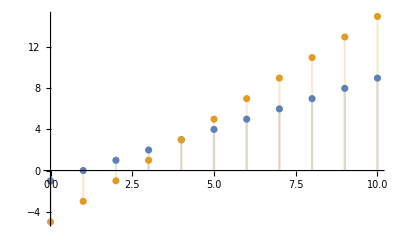

```mathematica
DiscretePlot[{m-1,2m-5},{m,0,10}]
```

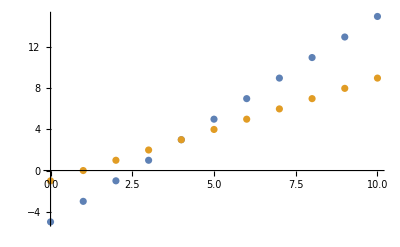

```mathematica
ListPlot[{Table[{m,2m-5},{m,0,10}],Table[{m,m-1},{m,0,10}]}]
```

```mathematica
sol=Solve[2m-n>0&&m-n>0&&m>0&&n>0&&n/m<1&&n/m>0,{m,n},Integers];
msol = m/.sol;
nsol=n/.sol;

msol
nsol
a=1;
b=2;
msol1=msol/.{C[1]->a,C[2]->b};
nsol1=nsol/.{C[1]->a,C[2]->b};
msol1
nsol1
CoprimeQ[msol1,nsol1]
```

{ConditionalExpression[2+C[1]+C[2],(C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥0]}

{ConditionalExpression[1+C[2],(C[1]|C[2])∈Integers&&C[1]≥0&&C[2]≥0]}

{5}

{3}

{True}

```mathematica
Co
```

```mathematica
Solve
```

```mathematica
Clear["Global`*"]
n=1;
m=3;
poly1=x^(2m-n)+λ  n/m - b  x^(m-n);
poly1//TraditionalForm
Solve[x^(2m-n)==-λ n/m,x]
```

-b x^2+λ/3+x^5

{{x→(-1/3)^(1/5) λ^(1/5)},{x→-λ^(1/5)/3^(1/5)},{x→-((-1)^(2/5) λ^(1/5))/3^(1/5)},{x→((-1)^(3/5) λ^(1/5))/3^(1/5)},{x→-((-1)^(4/5) λ^(1/5))/3^(1/5)}}

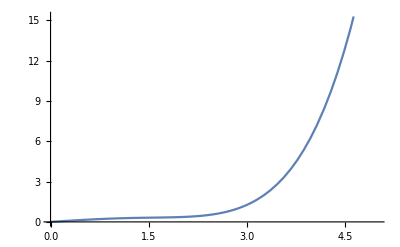

```mathematica
Clear["Global`*"]
a0=(-λ^(1/5)/3^(1/5));
S[ϵ_,nmax_]:=If[nmax==Infinity,Sum[a[n]*ϵ^n,{n,1,nmax}],Sum[a[n]*ϵ^n,{n,1,nmax}]+O[ϵ]^(nmax+1)]

k=10;
eqn=Collect[Normal[-b*ϵ*(a0+S[ϵ,k])^2+λ/3+(a0+S[ϵ,k])^5],ϵ];
coeflist= CoefficientList[eqn,ϵ];
coefsol=Solve[coeflist==0,Table[a[n],{n,1,k}]];
coefs=Table[a[n],{n,1,k}]/.coefsol[[1]];
xapprox[B_,Λ_]:=Total[coefs]/.{b->B,λ->Λ};
```